## ARMSupport

This file provides supporting functions for Analytical R-Matrix calculations.

## Version history

Initial set-up – pulling functions from a nebulous cloud of files.

- Made error handling on coulombCorrection more flexible by allowing for customized ReportingFunction. 
 - Fixed options handling on coulombCorrection (gave an error if no option was given).

Added v2Tolerance as an option for closestApproachTimesPath.

Fixed classicalClosestApproach - it gave wrong times for some reason.

Added new exception to path chooser - turning point on -π/2<Re(ωt)<π/2 to help avoid Re((r_cl(t))^2)<0 regions.

Added rInit support to trajectory functions.

Added non-standard t_s support to trajectory functions (i.e. forcets).

Added package export functionality.

Sealed off implementations inside `Private` contexts.

Changed order of documentation and `Private` sections to ensure public symbols do not end up as `Private`.

SetSharedFunction calls set to evaluate only on master kernel evaluation.

## Export features

#### To Quantum Optics Dynamic Dashboard

```mathematica
Block[{directory},
directory=Which[$MachineName=="ph-dtc11-09","D:\\Work\\CQD\\Project\\Code\\QuODD\\",True,"~/Work/CQD/Project/Code/QuODD/"];
Column[{
CopyFile[NotebookFileName[],directory<>"ARMSupport.nb",OverwriteTarget->True],
CopyFile[StringReplace[NotebookFileName[],".nb"->".m"],directory<>"ARMSupport.m",OverwriteTarget->True]
}]]
```

D:\Work\CQD\Project\Code\QuODD\ARMSupport.nb
D:\Work\CQD\Project\Code\QuODD\ARMSupport.m

#### To LES paper

```mathematica
With[{directory="/home/episanty/Work/CQD/Project/Papers/Contour freedom and low energy structures/Physics paper/"},Column[{
CopyFile[NotebookFileName[],directory<>"ARMSupport.nb",OverwriteTarget->True],
CopyFile[StringReplace[NotebookFileName[],".nb"->".m"],directory<>"ARMSupport.m",OverwriteTarget->True]
}]];
```

## General functions

#### Sundry initialization

```mathematica
BeginPackage["ARMSupport`",{"EPToolbox`"}]
```

ARMSupport`

```mathematica
stdpars={0.05,0.055,1.007};
```

```mathematica
r0={0,0,0};
```

This needs to be run before any parallel evaluation:

```mathematica
ParallelEvaluate[Needs["EPToolbox`","/home/episanty/Work/CQD/Project/Code/EPToolbox/EPToolbox/EPToolbox.m"]];
```

#### t_s and relatives

```mathematica
ts::usage="ts[{po, py, pp}, {F, ω, κ}] Returns the saddle point t_s directly.

ts[pp, κ, ω, F, po, py] Returns the saddle point t_s directly.";
t0::usage="t0[{po, py, pp}, {F, ω, κ}] Returns t_0=Re[t_s] directly.

t0[pp, κ, ω, F, po, py] Returns t_0=Re[t_s] directly.";
τ::usage="τ[{po, py, pp}, {F, ω, κ}] Returns τ_T=Im[t_s] directly.

τ[pp, κ, ω, F, po, py] Returns τ_T=Im[t_s] directly.";
tκ::usage="tκ[{po, py, pp}, {F, ω, κ}] Returns the starting point t_κ directly.

tκ[pp, κ, ω, F, po, py] Returns the starting point t_κ directly.";
```

```mathematica
Begin["`Private`"]
ts[pp_,κ_,ω_,F_,po_,py_]:=1/ω ArcSin[ω/F pp+ⅈ ω/F √(κ^2+po^2+py^2)]
ts[{po_,py_,pp_},{F_,ω_,κ_}]:=ts[pp,κ,ω,F,po,py]

t0[{po_,py_,pp_},{F_,ω_,κ_}]:=Re[ts[pp,κ,ω,F,po,py]]
t0[pp_,κ_,ω_,F_,po_,py_]:=Re[ts[pp,κ,ω,F,po,py]]

τ[{po_,py_,pp_},{F_,ω_,κ_}]:=Im[ts[pp,κ,ω,F,po,py]]
τ[pp_,κ_,ω_,F_,po_,py_]:=Im[ts[pp,κ,ω,F,po,py]]

tκ[pp_,κ_,ω_,F_,po_,py_]:=ts[pp,κ,ω,F,po,py]-ⅈ/κ^2
tκ[{po_,py_,pp_},{F_,ω_,κ_}]:=tκ[pp,κ,ω,F,po,py]
End[]
```

## Transition times and momenta

Classical transition times are those times t_r for which a classical orbit has a recollision at zero velocity: v(t_r)=0 and Re[∫_t_κ^t_r p+A(τ)ⅆτ]=0.

### Classical transitions times and momenta

getClassical Transition returns exact numerical solutions.

#### getClassicalTransition

```mathematica
getClassicalTransition::usage="getClassicalTransition[n, {F, ω, κ}] Returns pz and tr in atomic units as a list of replacement rules.
getClassicalTransition[range, {F, ω, κ}]
getClassicalTransition[n, F, ω, κ]";
```

```mathematica
pz::usage="pz represents the z component of momentum."
tr::usage="tr represents the return time as calculated by getClassicalTransition and friends."
```

```mathematica
Begin["`Private`"]
getClassicalTransition[n_,{F_,ω_,κ_}]:=getClassicalTransition[n,F,ω,κ]
getClassicalTransition[range_List,{F_,ω_,κ_}]:=(getClassicalTransition[#,{F,ω,κ}]&/@range)
getClassicalTransition[n_,F_,ω_,κ_]:=Module[{getTimes,t00,zinit},
getTimes[pz_]:=({t0->Re[#],τ->Im[#]}&[1/ω ArcSin[ω/F(pz+ⅈ κ)]]);
t00[pz_?NumericQ]:=(t0/.getTimes[pz]);
zinit[pz_?NumericQ]:=Re[F/ω^2(Cos[ω t0]-Cos[ω (t0+ⅈ τ-ⅈ/κ^2)])/.getTimes[pz]];
FindRoot[
{pz(tr-t00[pz])+F/ω^2(Cos[ω tr]-Cos[ω t00[pz]])+zinit[pz]==0,
pz-F/ω Sin[ω tr]==0}
,{{pz,0},{tr,(n+1)π/ω}}
]
]
End[]
```

```mathematica
getClassicalTransition[Range[8],stdpars]
```

{{pz→0.062865,tr→115.498},{pz→0.241791,tr→166.465},{pz→0.0314275,tr→229.108},{pz→0.142337,tr→282.741},{pz→0.0209511,tr→343.138},{pz→0.101158,tr→397.812},{pz→0.0157131,tr→457.273},{pz→0.0785167,tr→512.507}}

#### Benchmarking

Momentum against time.

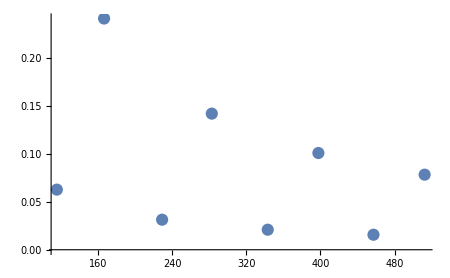
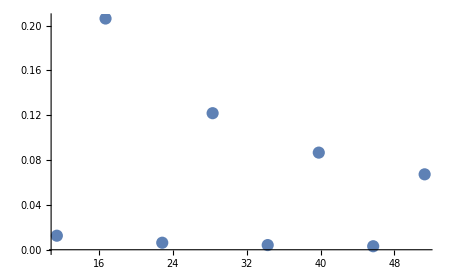

```mathematica
Row[{
ListPlot[{tr,pz}/.getClassicalTransition[Range[8],{0.05,0.055,1.007}],ImageSize->450],
ListPlot[{tr,pz}/.getClassicalTransition[Range[8],{10 0.05,10 0.055,1.007}],ImageSize->450]
}]
```

Normalized momentum against γ.

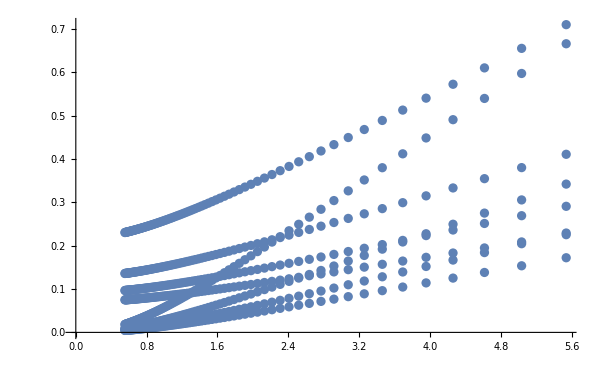

```mathematica
ListPlot[
Flatten[Table[
Block[{ω=0.055,κ=1.007},
{(ω κ)/F,(ω pz)/F}/.getClassicalTransition[Range[8],{F,ω,κ}]
]
,{F,0.01,0.1,0.001}],1]
,ImageSize->600
]
```

#### Sandbox

You’re probably here to calculate classical transitions for some given parameters. Have a go.

```mathematica
pz/.getClassicalTransition[Range[4],{0.05,45.6/3100,1.07}]
```

{0.0240298,0.755595,0.0120147,0.446211}

```mathematica
27.2 pz^2/2/.getClassicalTransition[Range[4],{0.05,45.6/3100,1.07}]
```

{0.00785306,7.76456,0.0019632,2.70781}

### Linearized solutions.

These functions return classical transition times which have been linearized to first order in p, i.e. p_z=F/ω((-1)^n+√(1+γ^2))/((n+1)π). The reduced results return ω/F p.

#### getLinearizedTransition

```mathematica
getLinearizedTransition::usage="getLinearizedTransition[n, {F, ω, κ}] Returns pz and tr in atomic units as a list of replacement rules.
getLinearizedTransition[range, {F, ω, κ}]
getLinearizedTransition[n, F, ω, κ]";
```

```mathematica
Begin["`Private`"]
getLinearizedTransition[n_,{F_,ω_,κ_}]:=getClassicalTransition[n,F,ω,κ]
getLinearizedTransition[range_List,{F_,ω_,κ_}]:=(getClassicalTransition[#,{F,ω,κ}]&/@range)
getLinearizedTransition[n_,F_,ω_,κ_]:={pz->F/ω getReducedLinearizedTransition[n,(ω κ)/F],tr->1/ω((n+1)π+ArcSin[getReducedLinearizedTransition[n,(ω κ)/F]])}
End[]
```

#### getReducedLinearizedTransition

```mathematica
getReducedLinearizedTransition::usage="getReducedLinearizedTransition[n, {F, ω, κ}] Returns ωpz/F directly.
getReducedLinearizedTransition[range, {F, ω, κ}]
getReducedLinearizedTransition[n, F, ω, κ]";
```

```mathematica
Begin["`Private`"]
getReducedLinearizedTransition[range_List,γ_]:=(getReducedLinearizedTransition[#,γ]&/@range)
getReducedLinearizedTransition[n_,γ_]:=((-1)^n+√(1+γ^2))/(π(n+1))
End[]
```

#### Full transitions. getFullLinearizedTransition and getFullReducedLinearizedTransition.

i.e. without neglecting terms in ω/κ^2.

```mathematica
getFullLinearizedTransition::usage="getFullLinearizedTransition[n, {F, ω, κ}] Returns pz and tr in atomic units as a list of replacement rules, for the linearized case without neglecting ω/κ^2.
getFullLinearizedTransition[range, {F, ω, κ}]
getFullLinearizedTransition[n, F, ω, κ]";
getFullReducedLinearizedTransition::usage="getFullReducedLinearizedTransition[n, {F, ω, κ}] Returns ωpz/F directly.
getFullReducedLinearizedTransition[range, {F, ω, κ}]
getFullReducedLinearizedTransition[n, F, ω, κ]";
```

```mathematica
Begin["`Private`"]
getFullLinearizedTransition[n_,{F_,ω_,κ_}]:=getFullLinearizedTransition[n,F,ω,κ]
getFullLinearizedTransition[range_List,{F_,ω_,κ_}]:=(getFullLinearizedTransition[#,{F,ω,κ}]&/@range)
getFullLinearizedTransition[n_,F_,ω_,κ_]:={pz->F/ω getFullReducedLinearizedTransition[n,(ω κ)/F],tr->1/ω((n+1)π+ArcSin[getReducedLinearizedTransition[n,(ω κ)/F]])}
getFullReducedLinearizedTransition[range_List,F_,ω_,κ_]:=(getFullReducedLinearizedTransition[#,F,ω,κ]&/@range)
getFullReducedLinearizedTransition[n_,F_,ω_,κ_]:=((-1)^n+√(1+((ω κ)/F)^2)Cosh[ω/κ^2]-(ω κ)/F Sinh[ω/κ^2])/((n+1)π)
End[]
```

#### Benchmarking

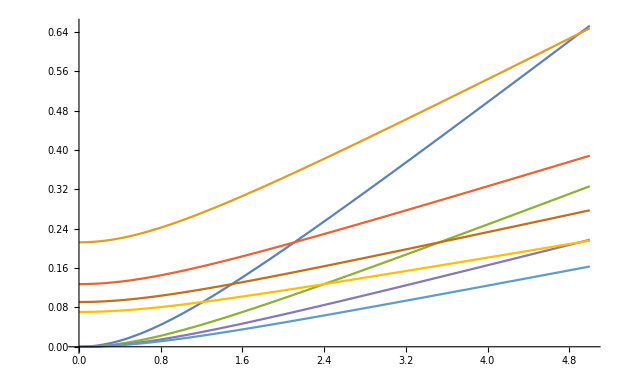

```mathematica
Plot[Evaluate@getReducedLinearizedTransition[Range[8],γ],{γ,0,5}]
```

### Complex-momentum solutions.

Complex-momentum solutions return complex times and momenta which are solutions to the complex equations v(t_r)=0  and ∫_t_κ^t_r p+A(τ)ⅆτ=0.

#### getComplexTransition

```mathematica
getComplexTransition::usage="getComplexTransition[n, {F, ω, κ}] Returns pz and tr in atomic units as a list of replacement rules.
getComplexTransition[range, {F, ω, κ}]
getComplexTransition[n, F, ω, κ]";
```

```mathematica
Begin["`Private`"]
getComplexTransition[n_,{F_,ω_,κ_}]:=getComplexTransition[n,F,ω,κ]
getComplexTransition[range_List,{F_,ω_,κ_}]:=(getComplexTransition[#,{F,ω,κ}]&/@range)
getComplexTransition[n_,F_,ω_,κ_]:=Module[{tκκ},
tκκ[pz_]:=ts[pz,κ,ω,F,0,0]-ⅈ/κ^2;
FindRoot[
(ω pz)/F((n+1) π+ArcSin[(ω pz)/F]-ω tκκ[pz])+(-1)^(n+1)√(1-((ω pz)/F)^2)-Cos[ω tκκ[pz]]==0
,{pz,0.0}]
]
End[]
```

```mathematica
getComplexTransition[Range[2],stdpars]
```

{{pz→0.0627928+0.00212574 ⅈ},{pz→0.228599+0.00501516 ⅈ}}

#### Benchmarking

```mathematica
AbsoluteTiming[
complexTransitionsBenchmarkingData=Flatten[Table[
Block[{F=0.05,κ=1.007},
{"k"->k,"γ"->(ω κ)/F,"ωpF"->(ω pz)/F}/.getComplexTransition[k,{F,ω,κ}]
]
,{k,1,8},{ω,0.001,0.5,0.001}],1];
]
```

{3.32934,Null}

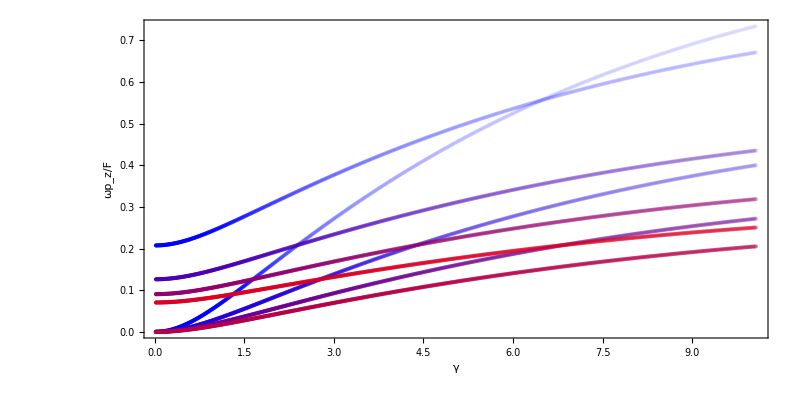

-Graphics-

```mathematica
Show[
Graphics[
{Quiet[Blend[{Blue,Red},("k"-2)/7]],Opacity[1/(1+Im["ωpF"]/0.01)],Point[{"γ",Re["ωpF"]}]}/.complexTransitionsBenchmarkingData
]
,FrameLabel->{"γ","ωp_z/F"},PlotRangePadding->None,Frame->True,ImageSize->{800,400},AspectRatio->0.5
]
```

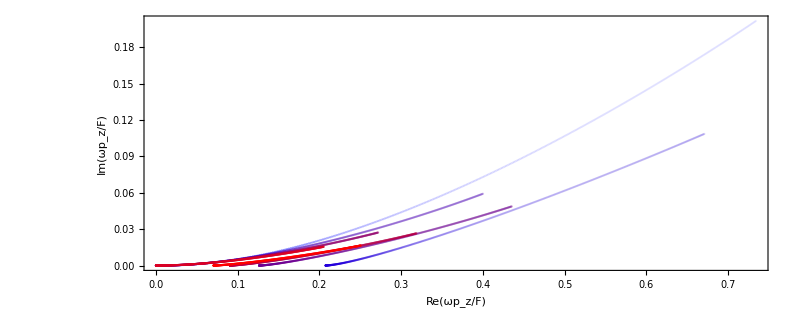

```mathematica
Graphics[
{Quiet[Blend[{Blue,Red},("k"-1)/7]],Opacity[1/(1+Im["ωpF"]/0.01)],PointSize[0.002],Point[{Re["ωpF"],Im["ωpF"]}]}/.complexTransitionsBenchmarkingData
,PlotRangePadding->0.1,Frame->True,Axes->{True,True},AxesOrigin->{0,0},FrameLabel->{"Re(ωp_z/F)","Im(ωp_z/F)"},ImageSize->800
]
```

```mathematica
-Graphics-.
```

### Comparison

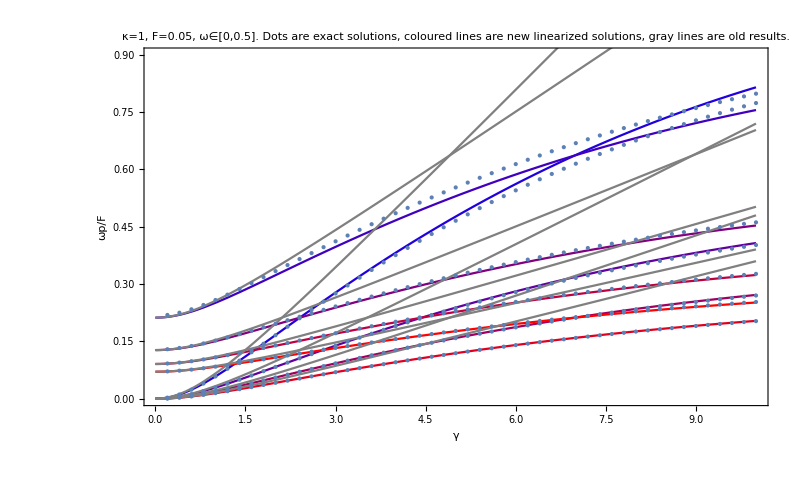

```mathematica
Block[{F=0.05,κ=1},Show[Table[
ParametricPlot[
Tooltip[
{(ω κ)/F,getFullReducedLinearizedTransition[n,F,ω,κ]}
,n]
,{ω,0.0,0.5},PlotStyle->Blend[{Blue,Red},n/8]
,Frame->True,PlotRangePadding->None,Axes->False,AspectRatio->0.6,ImageSize->800,FrameLabel->{"γ","ωp/F"}
,PlotLabel->"κ=1, F=0.05, ω∈[0,0.5]. Dots are exact solutions, coloured lines are\n new linearized solutions, gray lines are old results."
]
,{n,1,8}]~Join~Table[
ParametricPlot[
Tooltip[
{(ω κ)/F,getReducedLinearizedTransition[n,(ω κ)/F]}
,n]
,{ω,0.0,0.5},PlotStyle->Gray
]
,{n,1,8}]~Join~{
ListPlot[
Flatten[Table[
{(ω κ)/F,(ω pz)/F}/.getClassicalTransition[Range[8],{F,ω,κ}]
,{ω,0.01,0.5,0.01}],1]
,PlotStyle->PointSize[Medium]
]
},PlotRange->{{0.01,10},{0,0.9}}]]
```

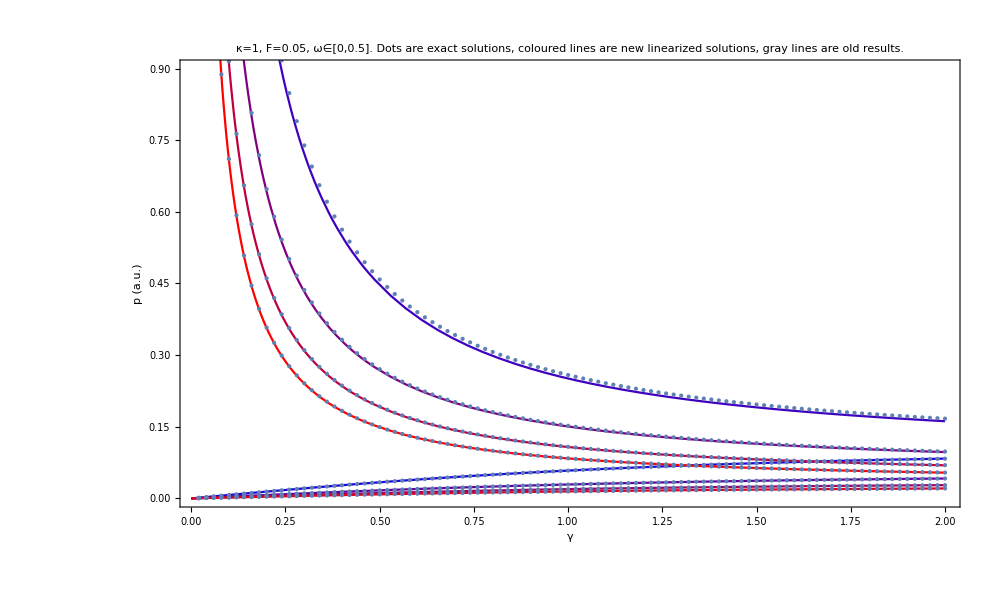

```mathematica
Block[{F=0.05,κ=1},Show[Table[
ParametricPlot[
Tooltip[
{(ω κ)/F,F/ω getFullReducedLinearizedTransition[n,F,ω,κ]}
,n]
,{ω,0.0,0.1},PlotStyle->Blend[{Blue,Red},n/8]
,Frame->True,PlotRangePadding->None,Axes->False,AspectRatio->0.6,ImageSize->1000,FrameLabel->{"γ","p (a.u.)"}
,PlotLabel->"κ=1, F=0.05, ω∈[0,0.5]. Dots are exact solutions, coloured lines are\n new linearized solutions, gray lines are old results."
]
,{n,1,8}]~Join~{
ListPlot[
Flatten[Table[
{(ω κ)/F,F/ω(ω pz)/F}/.getClassicalTransition[Range[8],{F,ω,κ}]
,{ω,0.001,0.1,0.001}],1]
,PlotStyle->PointSize[Medium]
]
},PlotRange->{{0.01,2},{0,0.9}}]]
```

## Trajectories

#### complexTrajectory

Returns r_cl(t)=∫_t_s^t_r p+A(τ)ⅆτ.

```mathematica
complexTrajectory::usage="complexTrajectory[t,{px,py,pz},{F,ω,κ}] Returns the vector-valued complex trajectory r_cl(t)=∫_t_s^t (p+A(τ))ⅆτ.

complexTrajectory[t,pz,{F,ω,κ}] Returns the z component of the complex trajectory z_cl(t)=∫_t_s^t (p_z+A(τ))ⅆτ.";
```

```mathematica
rInit::usage="rInit is an option for complexTrajectory and classicalTrajectory which specifies the initial position for the trajectory at time t_s.";
zInit::usage="zInit is an option for complexTrajectory and classicalTrajectory which specifies the initial z position for the trajectory at time t_s.";
forcets::usage="forcets is an option for complexTrajectory and classicalTrajectory which specifies a start time t_s to use for the trajectory, or uses the Automatic one.";
Protect[rInit,zInit,forcets];
```

```mathematica
Begin["`Private`"]
Options[complexTrajectory]={zInit->0,rInit->{0,0,0},forcets->Automatic};
complexTrajectory[t_,pz_,{F_,ω_,κ_},OptionsPattern[]]:=With[{tss=If[OptionValue[forcets]===Automatic,ts[{0,0,pz},{F,ω,κ}],OptionValue[forcets]]},
OptionValue[zInit]+pz(t-tss)+F/ω^2(Cos[ω t]-Cos[ω tss])
]
complexTrajectory[t_,{px_,py_,pz_},{F_,ω_,κ_},OptionsPattern[]]:=With[{tss=If[OptionValue[forcets]===Automatic,ts[{px,py,pz},{F,ω,κ}],OptionValue[forcets]]},
OptionValue[rInit]+{px,py,pz}(t-tss)+{0,0,1}F/ω^2(Cos[ω t]-Cos[ω tss])
]
End[]
```

#### classicalTrajectory

Returns Re[r_cl(t)]=Re[∫_t_s^t_r p+A(τ)ⅆτ].

```mathematica
classicalTrajectory::usage="classicalTrajectory[t, {px, py, pz}, {F, ω, κ}] Returns the real part of the vector-valued complex trajectory, Re(r_cl(t))=Re(∫_t_s^t (p+A(τ))ⅆτ).

classicalTrajectory[t, pz, {F, ω, κ}] Returns the real part of the z component  of the complex trajectory, Re(z_cl(t))=Re(∫_t_s^t (p_z+A(τ))ⅆτ).";
```

```mathematica
Begin["`Private`"]
classicalTrajectory[t_,pz_,{F_,ω_,κ_},OptionsPattern[zInit->0]]:=Re[complexTrajectory[t,pz,{F,ω,κ},zInit->OptionValue[zInit]]]
classicalTrajectory[t_?NumericQ,{px_,py_,pz_},{F_,ω_,κ_},OptionsPattern[rInit->0]]:=Re[complexTrajectory[t,{px,py,pz},{F,ω,κ},rInit->OptionValue[rInit]]]
End[]
```

## Closest Approach times

### Classical t_CAs

#### classicalClosestApproach

Returns a list of the classical closest approach times in the specified Range, in atomic units. These are solutions of the equation Re[r_cl(t)]·v(t)=Re[r_init+∫_t_s^t p+A(τ)ⅆτ]·v(t)=0 and are all real valued.

```mathematica
classicalClosestApproach::usage="classicalClosestApproach[{px, py, pz}, {F, ω, κ}] Returns t_CA, such that Re[r_cl(t_CA)]·v(t_CA)=0, for the given momentum and parameters. Accepts \"rules\" as an option, as well as \"Range\" in the format {t1, t2}, where both can contain the laser period \"T\".";
```

```mathematica
Begin["`Private`"]
Options[classicalClosestApproach]={"rules"->Automatic,"Range"->{0,2"T"}};
classicalClosestApproach[{px_,py_,pz_},{F_,ω_,κ_},OptionsPattern[]]:=Module[
{tstart,zinit},
tstart=If[NumberQ[OptionValue["rules"]],
"t0"/.OptionValue["rules"],
Re[1/ω ArcSin[ω/F(pz+ⅈ √(κ^2+px^2+py^2))]]
];
zinit=F/ω^2 Cos[ω tstart]-F/ω^2 Re[Cos[ArcSin[ω/F(pz+ⅈ √(κ^2+px^2+py^2))]]];
If[Length[#]>0,t/.#,{}]&@Quiet[
NSolve[{
{px,py,pz-F/ω Sin[ω t]}.classicalTrajectory[t,{px,py,pz},{F,ω,κ}]==0,
Evaluate[OptionValue["Range"]⟦1⟧<t<OptionValue["Range"]⟦2⟧/.{"T"->(2π)/ω}]
},t]
]
]
End[]
```

#### rDotV

Returns the value of Re[r_cl(t)]·v(t)=Re[r_init+∫_t_s^t p+A(τ)ⅆτ]·v(t) for the specified time, momentum and parameters. Useful mainly as a cleaner way to plot its zero contours - i.e. the surfaces formed by the t_CA on different geometrical spaces.

```mathematica
rDotV::usage="rDotV[t, px, pz, {F, ω, κ}] Returns the classical r(t)·v(t) for the given momentum and parameters.";
```

```mathematica
Begin["`Private`"]
rDotV[t_,{px_,py_,pz_},{F_,ω_,κ_}]:=Module[{tss,zinit=F/ω^2(1-√(1+((κ ω)/F)^2))},
tss=If[NumberQ[OptionValue["rules"]],
"t0"/.OptionValue["rules"],
Re[1/ω ArcSin[ω/F(pz+ⅈ √(κ^2+px^2+py^2))]]
];
(px^2+py^2)(t-tss)+(pz(t-tss)+F/ω^2(Cos[ω t]-Cos[ω tss])+zinit)(pz-F/ω Sin[ω t])
]
End[]
```

Two-dimensional version memoized for efficiency:

```mathematica
Begin["`Private`"]
rDotV[t_,px_,pz_,{F_,ω_,κ_}]:=rDotV[t,px,pz,{F,ω,κ}]=rDotV[t,{px,0,pz},{F,ω,κ}]
End[]
```

#### d2r2

Returns the second derivative d^2/dt^2[(r_cl(t))^2]=d^2/dt^2[(Re(r_init+∫_t_s^t p+A(τ)ⅆτ))^2].

```mathematica
d2r2::usage="d2r2[t, {px, py, pz}, {F, ω, κ}] Returns the classical second time derivative d^2/dt^2r_cl^2 at the given momentum and parameers.";
```

```mathematica
Begin["`Private`"]
d2r2[t_,{px_,py_,pz_},{F_,ω_,κ_}]:=d2r2[t,{px,py,pz},{F,ω,κ}]=2(Norm[{px,py,pz}-{0,0,1}F/ω Sin[ω t]]^2-classicalTrajectory[t,pz,{F,ω,κ}]F Cos[ω t])
End[]
```

### Quantum t_CAs

are the complex solutions of r_cl(t)·v(t)=(r_init+∫_t_s^t p+A(τ)ⅆτ)·v(t)=0.

#### allQuantumClosestApproachTimes

```mathematica
allQuantumClosestApproachTimes::usage="allQuantumClosestApproachTimes[{px, py, pz}, {F, ω, κ}, {xinit, yinit, zinit}] returns the quantum tCAs as a list of complex values. It accepts as options an explicit \"ts\" and a \"Range\", set to {-2ⅈτ, T+2ⅈτ} by default, as well as all the options of EPToolbox`FindComplexRoots.";
tCA::usage="tCA represents a closest approach time t_CA.";
```

```mathematica
Begin["`Private`"]
Options[allQuantumClosestApproachTimes]=Join[Options[FindComplexRoots],{"rules"->Automatic,"Range"->Automatic}];
allQuantumClosestApproachTimes[{po_,py_,pp_},{F_,ω_,κ_},{xinit_,yinit_,zinit_},options:OptionsPattern[]]:=Module[
{tss,range,rules},
tss=If[OptionValue["rules"]===Automatic,ts[pp,κ,ω,F,po,py],"ts"/.OptionValue["rules"]];
rules=If[OptionValue["rules"]===Automatic,
{"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"->2π/ω},
OptionValue[rules]
];
range=Which[
MatchQ[OptionValue["Range"]/.rules,{a_?NumericQ,b_?NumericQ}/;Im[b-a]≤0],(OptionValue[Range]/.rules)+{-2ⅈ Im[tss],2ⅈ Im[tss]},
MatchQ[OptionValue["Range"]/.rules,{_?NumericQ,_?NumericQ}],(OptionValue[Range]/.rules),
True,{-2ⅈ Im[tss],(2π)/ω+2ⅈ Im[tss]}
];
Sort@FindComplexRoots[
2({xinit,yinit,zinit}+{po,py,pp}(tCA-tss)+{0,0,F/ω^2(Cos[ω tCA]-Cos[ω tss])}).{po,py,pp-F/ω Sin[ω tCA]}==0
,{tCA,range⟦1⟧,range⟦2⟧}
,Sequence@@FilterRules[{options},Options[FindComplexRoots]]
,Seeds->200
,Tolerance->10^(4-$MachinePrecision)
]
]
End[]
```

#### makeCircuitTCAsFromCircuit

Takes a ready-made circuit, in the format {{n_1, {p_(x 1), p_(y 1), p_(z 1)}}, ..., {n_N, {p_(x N), p_(y N), p_(z N)}}}, and calculates all the relevant t_CAs for it, returning the tags and the momentum in the output, which is of the form {{n_1, {p_(x 1), p_(y 1), p_(z 1)}, t_(CA 1 ,1)}, {{n_1, {p_(x 1), p_(y 1), p_(z 1)}, t_(CA 1 ,2)}, ..., {{n_N, {p_(x N), p_(y N), p_(z N)}, t_(CA N, k)}}.

```mathematica
makeTCAsFromCircuit::usage="makeTCAsFromCircuit[{{n1, {px1, py1, pz1}}, ..., {nN, {pxnN, pynN, pznN}}}, {F, ω, κ}, {xinit, yinit, zinit}] Calculates the tCAs for the given circuit and parameters. The ni can be any tags which are returned with the output, which is of the form {{n1, {px1, py1, pz1}, tCA11}, {n1, {px1, py1, pz1}, tCA12}, ..., {nN, {pxnN, pynN, pznN}, tCAnNk}}, with all the appropriate tCA in separate entries. Same \"rules\" and \"Range\" options as allQuantumClosestApproachTimes.";
```

```mathematica
Begin["`Private`"]
Options[makeTCAsFromCircuit]=Join[{"rules"->Automatic,OptionValue["Range"]->Automatic,PlotRange->Automatic},Options[allQuantumClosestApproachTimes]];
makeTCAsFromCircuit[circuit_,{F_,ω_,κ_},{xinit_,yinit_,zinit_},options:OptionsPattern[]]:=Module[
{range,rules,tss,n,pvec},
Flatten[ParallelTable[
{n,pvec}=element;
Needs["EPToolbox`","/home/episanty/Work/CQD/Project/Code/EPToolbox/EPToolbox/EPToolbox.m"];
tss=If[OptionValue["rules"]===Automatic,ts[pvec⟦1⟧,κ,ω,F,pvec⟦1⟧],"ts"/.OptionValue["rules"]];
rules=If[OptionValue["rules"]===Automatic,
{"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"->2π/ω},
OptionValue[rules]
];
range=Automatic;
range=Which[
MatchQ[OptionValue["Range"]/.rules,{_?NumericQ,_?NumericQ}],OptionValue["Range"]/.rules,
MatchQ[OptionValue[PlotRange]/.rules,{{_?NumericQ,_?NumericQ},{_?NumericQ,_?NumericQ}}],Complex@@@(OptionValue[PlotRange]ᵀ/.rules),
True,{-2ⅈ Im[tss],(2π)/ω+2ⅈ Im[tss]}
];(*ugly logic inside the Table because range depends on tss which depends on p*)
{n,pvec,tCA}/.allQuantumClosestApproachTimes[{pvec⟦1⟧,0,pvec⟦2⟧},{F,ω,κ},{xinit,yinit,zinit}
,Sequence@@FilterRules[{options},Options[allQuantumClosestApproachTimes]],"Range"->range
]
,{element,circuit}],1]
]
End[]
```

#### makeTCAsFromRange

Takes a specific range of momentum and gets all the relevant t_CAs for a rectangular grid of those specifications.

```mathematica
makeTCAsFromRange::usage="makeTCAsFromRange[{pomin, pomax, δpo}, {ppmin, ppmax, δpp}, fixedMomenta, {F, ω, κ}, {xinit, yinit, zinit}, \"Range\"→{t1, t2}] Returns a list with elements of the form {{po, py, pp}, tCA} for a rectangular grid in momentum with the given spans and separations. fixedMomenta should be a list of replacement rules such as {py→0}.";
```

```mathematica
Begin["`Private`"]
Options[makeTCAsFromRange]=Join[{"rules"->Automatic,OptionValue["Range"]},Options[allQuantumClosestApproachTimes]];
makeTCAsFromRange[{pomin_,pomax_,δpo_},{ppmin_,ppmax_,δpp_},fixedMomenta_,{F_,ω_,κ_},{xinit_,yinit_,zinit_},options:OptionsPattern[]]:=Module[
{range,rules,tss},
tss=If[OptionValue["rules"]===Automatic,ts[pp,κ,ω,F,po,py],"ts"/.OptionValue["rules"]];
rules=If[OptionValue["rules"]===Automatic,
{"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"->2π/ω},
OptionValue[rules]
];
Flatten[
Table[
range=Which[
MatchQ[OptionValue["Range"]/.rules/.fixedMomenta,{_?NumericQ,_?NumericQ}],OptionValue["Range"]/.rules,
MatchQ[OptionValue[PlotRange]/.rules/.fixedMomenta,{{_?NumericQ,_?NumericQ},{_?NumericQ,_?NumericQ}}],Complex@@@(OptionValue[PlotRange]ᵀ/.rules),
True,{-2ⅈ Im[tss],(2π)/ω+2ⅈ Im[tss]}
]/.fixedMomenta;(*ugly logic inside the Table because range depends on tss which depends on p*)
{{po,py,pp}/.fixedMomenta,tCA}/.allQuantumClosestApproachTimes[{po,py,pp}/.fixedMomenta,{F,ω,κ},{xinit,yinit,zinit}
,"Range"->range,Sequence@@FilterRules[{options},Options[allQuantumClosestApproachTimes]]
]
,{po,pomin,pomax,δpo},{pp,ppmin,ppmax,δpp}]
,{1,2,3}]
]
End[]
```

#### closestApproachTimesPath

uses magic to choose the appropriate t_CA’s the integration contour should pass through. Output is the same as allQuantumClosestApproachTimes.

```mathematica
closestApproachTimesPath::usage="closestApproachTimesPath[{px, py, pz}, {F, ω, κ}, {xinit, yinit, zinit}] Returns a selected and ordered list of complex tCAs as replacement rules, in atomic units. Accepts the same \"rules\" and \"Range\" options as allQuantumClosestApproachTimes.";
v2Tolerance::usage="v2Tolerance is an option for closestApproachTimesPath which determines the tolerance v2tol to be used when selecting tCAs for the path. Time tCA is included in the path if Re[v[tCA]^2]≥-v2tol.";Protect[v2Tolerance];
```

```mathematica
Begin["`Private`"]
Options[closestApproachTimesPath]=Join[{v2Tolerance->Automatic},Options[allQuantumClosestApproachTimes],Options[ListPlot]];
closestApproachTimesPath[{po_,py_,pp_},{F_,ω_,κ_},{xinit_,yinit_,zinit_},options:OptionsPattern[]]:=Module[
{tss,r,v,range,rules,v2tol},
tss=If[OptionValue["rules"]===Automatic,ts[pp,κ,ω,F,po,py],"ts"/.OptionValue["rules"]];
rules=If[OptionValue["rules"]===Automatic,
{"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"->2π/ω},
OptionValue[rules]
];
v2tol=Which[OptionValue[v2Tolerance]===Automatic,10^-8,True,OptionValue[v2Tolerance]];
r[tt_]:=({xinit,yinit,zinit}+{po,py,pp}(tt-tss)+{0,0,F/ω^2(Cos[ω tt]-Cos[ω tss])});
v[tt_]:=({po,py,pp}+{0,0,-F/ω Sin[ω tt]});
range=Which[
MatchQ[OptionValue["Range"]/.rules,{_?NumericQ,_?NumericQ}],OptionValue["Range"]/.rules,
MatchQ[OptionValue[PlotRange]/.rules,{{_?NumericQ,_?NumericQ},{_?NumericQ,_?NumericQ}}],Complex@@@(OptionValue[PlotRange]ᵀ/.rules),
True,{-2ⅈ Im[tss],(2π)/ω+2ⅈ Im[tss]}
];
Select[
Sort[
allQuantumClosestApproachTimes[{po,py,pp},{F,ω,κ},{xinit,yinit,zinit}
,"Range"->range
,Sequence@@FilterRules[{options},Options[allQuantumClosestApproachTimes]]
,Tolerance->10^(4-$MachinePrecision)],
((Re[tCA]/.#1)<(Re[tCA]/.#2))&
],
(Or[
And[1/4(2π)/ω<Re[tCA]<3/4(2π)/ω,Im[tCA]>0],
And[-1/4(2π)/ω<Re[tCA]<1/4(2π)/ω,Im[tCA]≥0,Im[Sin[ω tCA]]<ω κ/F],
And[(-0.3Im[tss]≤Im[tCA]<Im[tss]-1/κ^2),(Re[tCA]-0.1(2π)/ω>Re[tss]),(Re[v[tCA].v[tCA]]≥-v2tol)]
]/.#&)
]
]
End[]
(*closestApproachTimesPath[{0.05,0,1.2},stdpars,{0,0,0},"Range"->{-5ⅈ,5.6"T"+30ⅈ}]*)
```

## Amplitude-related functions

#### Volkov exponent

```mathematica
volkovExponent::usage="volkovExponent[{po, py, pp}, {F, ω, κ}] calculates Re(ⅈ∫_0^t_s (I_p+1/2(p+A(τ))^2)ⅆτ).";
```

```mathematica
Begin["`Private`"]
(*FullSimplify[Re[
ⅈ Integrate[κ^2/2+1/2(po^2+py^2)+1/2(pp-F/ω Sin[ω t])^2,{t,0,1/ω ArcSin[ω/F(pp+ⅈ √(κ^2+po^2+py^2))]}]/.{Sin[2u_]->2Sin[u]Cos[u]}
]]*)
volkovExponent[{po_,py_,pp_},{F_,ω_},κ_]:=-1/8 Im[1/ω^3(2 F ω (-4 pp+3 pp √(1+((-ⅈ pp+√(po^2+py^2+κ^2))^2 ω^2)/F^2)-ⅈ √(po^2+py^2+κ^2) √(1+((-ⅈ pp+√(po^2+py^2+κ^2))^2 ω^2)/F^2))+2 (F^2+2 (po^2+pp^2+py^2+κ^2) ω^2) ArcSin[((pp+ⅈ √(po^2+py^2+κ^2)) ω)/F])]
volkovExponent[{po_,py_,pp_},{F_,ω_,κ_}]:=volkovExponent[{po,py,pp},{F,ω},κ]
End[]
```

### coulombCorrection

Numerically integrates ∫_C 1/(√((r_cl(t))^2))ⅆt over the specified complex integration path C. Sows parameters when integration errors are encountered, and allows for softening of the Coulomb kernel if required.

#### Definition

```mathematica
coulombCorrection::usage="coulombCorrection[{px, py, pz}, {F, ω, κ}, path] Calculates the Coulomb correction integral over the specified path. The path is a list which may contain \"tκ\", \"ts\", \"t0\", \"τ\", \"tCApath\" and \"T\", which will be replaced by the appropriate points.";
coulombCorrection::intErrors="Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}=`1`";
Softening::usage="Softening is an option for coulombCorrection which specifies whether the Coulomb kernel should be softened by a length σ. It is set by default to None (σ=0), and it can be changed to Automatic (σ=1/κ) or a numeric value for σ.";
ReportingFunction::usage="ReportingFunction is an option for coulombCorrection to specify the reporting of error-producing inputs. It should speficy a function f, set by default to Sow, which will be called as f[{{po, py, pp}, {F, ω, κ}, path}] if the inputs produce any errors during the NIntegrate call. To print to a file use ReportToFile.";
ReportToFile::usage="ReportToFile[directory, file] returns a function which can be used as a value for ReportingFunction inside coulombCorrection.\n\nReportToFile[directory, file][expr] adds a line with expr (properly parsed to ASCII for spaces, backslashes and quote marks) to directory/file.";
```

```mathematica
Begin["`Private`"]
If[$KernelID==0,SetSharedFunction[Sow]];
Quiet[ReportingFunction=ReportingFunction;Softening=Softening;]
Protect[ReportingFunction];Protect[Softening];

Options[coulombCorrection]=Join[{Softening->None,ReportingFunction->Sow},Options[closestApproachTimesPath]];
coulombCorrection[{po_,py_,pp_},{F_,ω_,κ_},path_:{"tκ","t0"},options:OptionsPattern[]]:=Block[
{tss,iterator,rules,range,tCApath,int,σ},
σ=Which[NumberQ[OptionValue[Softening]],OptionValue[Softening],OptionValue[Softening]===Automatic,1/κ,True,0];(*Coulomb softening*)
tss=ts[pp,κ,ω,F,po,py];
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"->2π/ω};
range=({Re[First[path]]-2ⅈ"τ",Re[Last[path]]+2ⅈ"τ"}/.rules);
If[
!FreeQ[path,"tCApath"],
tCApath=Chop[tCA/.closestApproachTimesPath[{po,py,pp},{F,ω,κ},{0,0,0},Sequence@@FilterRules[{options},Options[closestApproachTimesPath]],"Range"->range]];
If[Length[tCApath]>0,
AppendTo[rules,"tCApath"->Apply[Sequence,tCApath]],
AppendTo[rules,"tCApath"->(##&[])]
]
];(*Print[rules];*)
iterator={t,Sequence@@Evaluate[path/.rules]};(*Print[iterator];*)
Check[
int=NIntegrate[-((po^2+py^2)(t-tss)^2+(pp(t-tss)+F/ω^2(Cos[ω t]-Cos[ω tss]))^2+σ^2)^(-1/2),Evaluate@iterator],
OptionValue[ReportingFunction][Chop[{{po,py,pp},{F,ω,κ},path}]];Message[coulombCorrection::intErrors,Chop[{{po,py,pp},{F,ω,κ},path}]];int
]
]
End[]
```

```mathematica
Begin["`Private`"]
ReportToFile[directory_,file_]:=Function[expr,Run["cd "<>directory<>" && echo "<>StringReplace[ToString[expr/.{s_String:>StringJoin["\"",s,"\""]},CharacterEncoding->"ASCII"],{" "->"\\ ","\\"->"\\\\","\""->"\\\""}]<>" >> "<>StringReplace[file,{" "->"\\ ","\\"->"\\\\","\""->"\\\""}]]]
End[]
```

#### Tests of the error handling

For a single evaluation

```mathematica
Reap[
coulombCorrection[{2,0,0},{0.05,0.055,1.007},{"tκ","t0"}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.  + 25.8533\ ⅈ}. NIntegrate obtained 2.67192  + 2.68596\ ⅈ and 0.0610813 for the integral and error estimates.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{2, 0, 0}, {0.05, 0.055, 1.007}, {"t\[Kappa]", "t0"}}

{2.67192+2.68596 ⅈ,{{{{2,0,0},{0.05,0.055,1.007},{tκ,t0}}}}}

Test of the error handling inside a Parallelized Table.

```mathematica
(*This needs to be run before any parallel evaluation.*)
ParallelEvaluate[Needs["EPToolbox`","/home/episanty/Work/CQD/Project/Code/EPToolbox/EPToolbox/EPToolbox.m"]];
```

```mathematica
Reap[
ParallelTable[
Quiet@coulombCorrection[{po,0,0},{0.05,0.055,1.007},{"tκ","t0"}]
,{po,-2,2,0.1}]
]⟦2,1⟧
(*Generates about 2 pages of errors if not Quieted. This shows the Reaped trouble inputs only.*)
```

{{{-1.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.4,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.1,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-2.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.3,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.5,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.2,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.1,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.3,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.5,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{2.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.2,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.4,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.8,0,0},{0.05,0.055,1.007},{tκ,t0}}}

Print errors to file:

```mathematica
coulombCorrection[{0.01,0,0.5},stdpars,{"tκ",2"T"},ReportingFunction->ReportToFile[NotebookDirectory[],"test.txt"]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {75.9294  + 11.9\ ⅈ}. NIntegrate obtained -7.48256 + 3.89417\ ⅈ and 0.00477198 for the integral and error estimates.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{0.01, 0, 0.5}, {0.05, 0.055, 1.007}, {"t\[Kappa]", 2\ "T"}}

-7.48256+3.89417 ⅈ

and then reimport from the file

```mathematica
ToExpression[Import[NotebookDirectory[]<>"test.txt"]]
coulombCorrection@@%
```

{{0.01,0,0.5},{0.05,0.055,1.007},{tκ,2 T}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {75.9294  + 11.9\ ⅈ}. NIntegrate obtained -7.48256 + 3.89417\ ⅈ and 0.00477198 for the integral and error estimates.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{0.01, 0, 0.5}, {0.05, 0.055, 1.007}, {"t\[Kappa]", 2\ "T"}}

-7.48256+3.89417 ⅈ

Printing to file from inside a parallelized environment. Note that parallelized kernels have no FrontEnd and therefore cannot access NotebookDirectory[].

```mathematica
Block[{directory=NotebookDirectory[]},
ParallelTable[
Quiet@coulombCorrection[{po,0,0},{0.05,0.055,1.007},{"tκ","t0"},ReportingFunction->ReportToFile[directory,"test.txt"]]
,{po,-2,2,0.1}];
]
```

```mathematica
ToExpression/@Import[NotebookDirectory[]<>"test.txt","List"]
coulombCorrection@@@%
```

{{{-1.4,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.1,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.3,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-2.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.2,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.5,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-0.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.1,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.7,0,0},{0.05,0.055,1.007},{tκ,t0}},{{-1.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.5,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.3,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.2,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.8,0,0},{0.05,0.055,1.007},{tκ,t0}},{{0.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.6,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.4,0,0},{0.05,0.055,1.007},{tκ,t0}},{{1.9,0,0},{0.05,0.055,1.007},{tκ,t0}},{{2.,0,0},{0.05,0.055,1.007},{tκ,t0}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.  + 18.639\ ⅈ}. NIntegrate obtained 2.37932  + 3.44132\ ⅈ and 0.074767 for the integral and error estimates.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{-1.4, 0, 0}, {0.05, 0.055, 1.007}, {"t\[Kappa]", "t0"}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.  + 22.5694\ ⅈ}. NIntegrate obtained 2.5598  + 3.02543\ ⅈ and 0.0520024 for the integral and error estimates.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{-1.7, 0, 0}, {0.05, 0.055, 1.007}, {"t\[Kappa]", "t0"}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.  + 13.7753\ ⅈ}. NIntegrate obtained 2.12149  + 3.84551\ ⅈ and 0.0406284 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

coulombCorrection::intErrors: Integration errors obtained at input {{po, py, pp}, {F, ω, κ}, path}={{-1.1, 0, 0}, {0.05, 0.055, 1.007}, {"t\[Kappa]", "t0"}}

General::stop: Further output of coulombCorrection :: intErrors will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{2.37932+3.44132 ⅈ,2.5598+3.02543 ⅈ,2.12149+3.84551 ⅈ,1.60378+4.39982 ⅈ,2.33519+3.5208 ⅈ,2.50409+3.16691 ⅈ,2.67192+2.68596 ⅈ,1.98033+4.00272 ⅈ,2.23833+3.67126 ⅈ,1.34139+4.5624 ⅈ,2.47792+3.24468 ⅈ,1.85702+4.16404 ⅈ,2.63455+2.79829 ⅈ,0.931087+4.7784 ⅈ,1.34139+4.5624 ⅈ,1.85702+4.16404 ⅈ,2.12149+3.84551 ⅈ,2.5598+3.02543 ⅈ,2.61225+2.91755 ⅈ,2.47792+3.24468 ⅈ,1.60378+4.39982 ⅈ,1.98033+4.00272 ⅈ,2.33519+3.5208 ⅈ,2.23833+3.67126 ⅈ,2.61225+2.91755 ⅈ,0.931087+4.7784 ⅈ,2.50409+3.16691 ⅈ,2.37932+3.44132 ⅈ,2.63455+2.79829 ⅈ,2.67192+2.68596 ⅈ}

## End of package

```mathematica
EndPackage[]
```